```mathematica
NotebookEvaluate[NotebookDirectory[]<>"NOMexplicitPhaseFieldMain.nb"];
```

```mathematica
xmin={-0.1,-0.1};xmax={0.1,0.};{width,height}=xmax-xmin;dx=height/400;
coord=GridNdim[xmin,xmax,dx];
```

```mathematica
plane1={-0.0255,1.,-0.0255,-0.05};plane2={0.0255,1.,0.0255,-0.05};
```

```mathematica
p1List=FindPointsC[coord,plane1[[3;;4]]-4 dx,plane2[[1;;2]]+4 dx];
p2List=FindPointsC[coord,plane1[[3;;4]]+4 dx,plane2[[1;;2]]-4 dx];
checkList=Complement[p1List,p2List];
```

```mathematica
NeiList0=Nearest[coord->Automatic,coord,30+1];
```

```mathematica
{NeiList2,broNei}=NeighborUpdateByPlane[NeiList0,coord,{plane1,plane2},SegmentListCut2P,checkList];
```

```mathematica
NeiList=NeiList2[[All,1;;9]];
```

```mathematica
(*Create the model*)

Nnode=Length[coord];ndim=Length[coord[[1]]];
ndof=ndim Nnode;vol=ConstantArray[dx dx,Nnode];
Es=190. 10^9;mu=0.3;rho=7800.;pmass=rho vol;etype=2;
dxList=ConstantArray[dx,Nnode];

Gc=22000.;ls=2dxList;pfModulus=4.;pfModulusT=1.;(*phase field length scale.*)
{bulkK,shearG}=PlaneStress[Es,mu,True];
penCoef=1.;
WeiF[r_]:=1./r^2;
coord0=coord;mesh1=MyDelaunayMesh[coord0];(*mesh for postprocess only*)
acc=ConstantArray[0.,{Nnode,ndim}];
accNew=acc;
internalF=acc;
velo=acc;
veloSound=Sqrt[Es/rho];tIncMax=Min[dxList]/veloSound;
ctime=0.;
tInc=0.8tIncMax;
TotalTime=10 tInc;
pfList=ConstantArray[0.,Nnode];
gradS=ConstantArray[0.,{Nnode,ndim}];lapS=pfList;
enerP=pfList;
uvw=0.;
deformList=0.;
```

```mathematica
neicoord0=NeighborPartitionC[coord0,NeiList];
neivol=NeighborPartitionC[vol,NeiList];
WeiF[r_]:=1./r^2;
neiWeiL=WeightByNeighborC2[neicoord0];
{trKList,invKList}=KmatrixL[neicoord0,neiWeiL,neivol];
```

```mathematica
(*nfix=FindPoints[coord,xmin-{0.5 dx,0.5 dx},xmin+{height+0.5 dx,0.5dx}];
nvelo=FindPoints[coord,xmax-{height+0.5 dx,0.5dx},xmax+{0.5 dx,0.5 dx}];
dofFix=ConstantArray[{0.,0.},Length[nfix]];(*dof in y direction*)
forceY={0.,1.};
veloValue=ConstantArray[forceY,Length[nvelo]];
nforce={};
dofForce={};
xmid=0.5 (xmin+xmax);
npf=FindPoints[coord,xmid-{0.5 width,1. dx},xmid+{0.,1 dx}];*)
nfix={};dxMean=Mean[dxList];
nvelo=FindPointsC[coord0,{-0.0255,-2 dxMean},{0.0255,dxMean}];
dofFix={};
forceY={0.,-16.5};
veloValue=ConstantArray[forceY,Length[nvelo]];
nforce={};
dofForce={};
xmid=0.5 (xmin+xmax);
npf={};
```

```mathematica
KineticEnergy={};
timeList={};
strainEnergy={};
pfEnergy={};
uMaxList={};
vMaxList={};
reactionForceList={};
jstep=1;
```

```mathematica
statisticInterval=10;outputInterval=40;printInterval=20;ls=2.dxList;
numstep=3000;

resiMaxList={};

fpath=CreateFolder[ToString[Gc]<>"KW2d uniform,800x400"<>ToString[IntegerPart[width/dxMean]]];gcl=0.;L2pfresidu=0.;L2pfInc=0.;pfInc=0.;tolL2pfInc=10.^-4;
tolpfIncMax=10.^-3;
resiMaxTol=10.^-2;subInterMax=20;
```

```mathematica
isAbortPath=fpath<>"isAbort.txt"
```

```mathematica
Do[coord+=tInc velo+(0.5 tInc^2)acc;
coord[[nfix]]=coord0[[nfix]]+dofFix;(*displacement constraint*)
velo[[nfix]]=0.;
uvw=coord-coord0;
neicoord=NeighborPartitionC[coord,NeiList];
neipfList=NeighborPartitionC[pfList,NeiList];
{gradS,deformList}=FSmatrixL[neipfList,neicoord,neicoord0,neivol,invKList,neiWeiL];
{enerP,enerN,stress,stressP}=StressList[ndim,bulkK,shearG,gcl,deformList];kMax=1;resiMax1=0.;
resiMax2=0.;
Do[
lapS=LaplaceSListAll[NeiList,neicoord0,gradS,neipfList,invKList,trKList,neivol,penCoef,neiWeiL];
lapS/=vol;
pfresi=PhaseFieldResidual[ls,Gc,lapS,pfList,enerP];
If[k==1,resiMax1=Max[pfresi]];
resiMax2=Max[pfresi];
AppendTo[resiMaxList,resiMax2];
L2pfInc=Sqrt[(pfresi vol).pfresi/Total[vol]];
If[k==1,pfModulusT=Max[pfModulus,20 resiMax1]];
pfList+=1./pfModulusT*pfresi;
(*If[Max[pfList]≥0.99,Print["Error,phase field exceeds 1."]];
Do[If[pfList[[i]]>1.,pfList[[i]]=1.],{i,Nnode}];*)


pfList[[npf]]=1.;kMax=k;
If[k==1 && resiMax1<resiMaxTol,Break[]];
If[resiMax2<tolpfIncMax || k==subInterMax,Break[],neipfList=NeighborPartitionC[pfList,NeiList];gradS=GradSmatrixL[neipfList,neicoord0,neivol,invKList,neiWeiL]];

(*If[L2pfInc<tolL2pfInc || k==subInterMax,Break[],neipfList=NeighborPartition[pfList,NeiList];gradS=GradSmatrixL[neipfList,neicoord0,neivol,invKList,neiWeiL]];*)

,{k,1,subInterMax}];
(*Print["subIteration:",kMax," resiMax:",resiMax2," resiMax0:",resiMax1];*)
stress+=((1.-pfList)^2-1.)stressP;
internalF=ForceListAllpf[NeiList,neicoord,neicoord0,stress,deformList,invKList,trKList,neivol,penCoef shearG,neiWeiL,pfList];
internalF[[nforce]]+=dofForce;(*add boundary forces to the internal force vector*) 
accNew=internalF/pmass;
velo+=0.5 tInc (acc+accNew);
velo[[nvelo]]=If[ctime<10.^-6,ctime/10.^-6,1.]veloValue;(*velocity constraint*)
accNew[[nvelo]]=0.;
accNew[[nfix]]=0.;
acc=accNew;

ctime+=tInc;jstep++;
If[Mod[jstep,statisticInterval]==1,AppendTo[timeList,ctime];AppendTo[KineticEnergy,0.5 pmass .Table[velo[[i]].velo[[i]],{i,Length[velo]}]];AppendTo[strainEnergy,StrainEnergyCal[enerP,enerN,vol,pfList]];AppendTo[pfEnergy,Gc (PhaseFieldEnergy[pfList,gradS,ls,vol])];
AppendTo[reactionForceList,Total[internalF[[nfix]]]]];
If[Mod[jstep,printInterval]==1,Print["acc max:",Max[accNew],",vel max:",Max[velo],",umax: ",Max[uvw]];
Print["step=",jstep,",t=",ctime," done"];Print[Plot2DField[uvw[[All,2]],mesh1]];Print[Plot2DField[velo[[All,2]],mesh1]];Print[Plot2DField[pfList,mesh1]]];
If[Mod[jstep,outputInterval]==1,OvitoOutput[fpath,"res",jstep,"x y ux uy pf vx vy",coord0,coord-coord0,pfList,velo];];CheckTextCommand[isAbortPath];
(*Print[Plot2DField[pfList,mesh1]]*)
,{i,numstep}];
Plot2DField[pfList,mesh1]
ListPlot[Log10[resiMaxList[[2;;]]],PlotRange->All]
```

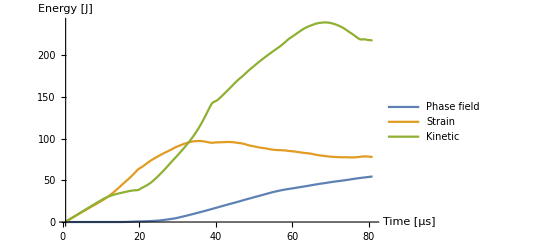

```mathematica
axesLabel={"Time [μs]","Energy [J]"};PlotXYL[timeList[[2;;len]] 10^6,pfEnergy[[2;;len]]/100,"Phase field",timeList[[2;;len]] 10^6,strainEnergy[[2;;len]]/100,"Strain",timeList[[2;;len]] 10^6,KineticEnergy[[2;;len]]/100,"Kinetic"]
```

```mathematica
pfE=pfEnergy[[1;;200]]/2;
pfE*=0.07981333293569341/Max[pfE];
```

```mathematica
dpfE=Table[pfE[[i]]-pfE[[i-1]],{i,2,Length[pfE]}];
vdc=dpfE/(10 tInc);
```

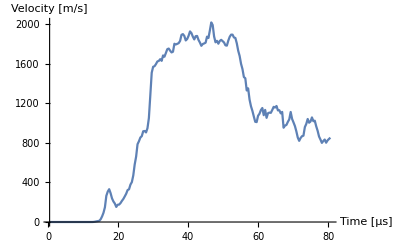

```mathematica
axesLabel={"Time [μs]","Velocity [m/s]"};PlotXYL[10^6 timeList[[1;;Length[vdc]]],vdc,""]
```

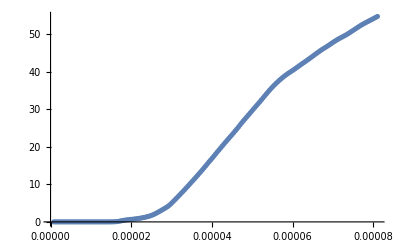

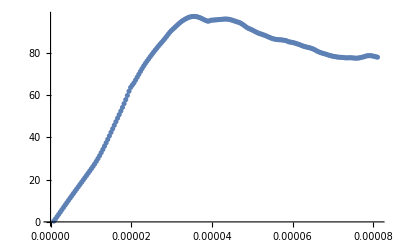

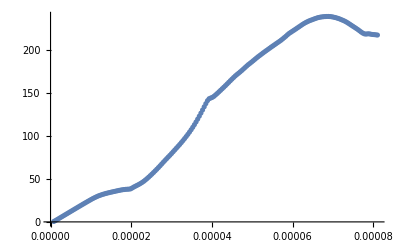

-Graphics-

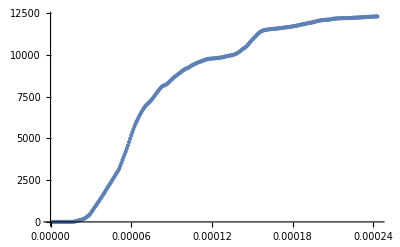

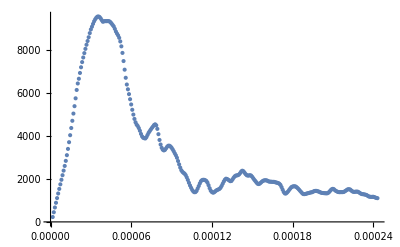

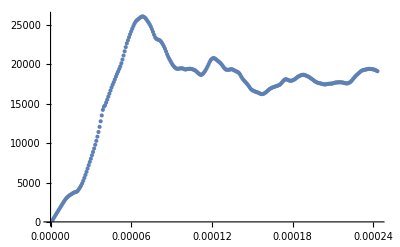

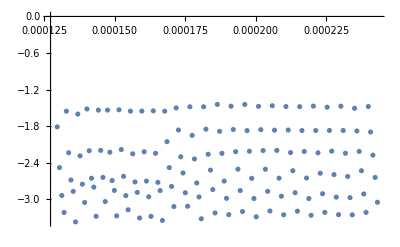

```mathematica
len=200;ListPlot[{timeList[[2;;len]],pfEnergy[[2;;len]]/100}ᵀ]
ListPlot[{timeList[[2;;len]],strainEnergy[[2;;len]]/100}ᵀ]
ListPlot[{timeList[[2;;len]],KineticEnergy[[2;;len]]/100}ᵀ]
ListPlot[{timeList[[2;;len]],Log10[resiMaxList[[2;;len]]]}ᵀ]
```